# FFPlanet tools

## Ejecting planets CDF fitting

## data

```mathematica
epsdata={{404.547,360.82,409.801,30.2,0,90.398,107.398,30.203,0,90.399,83.204,30.199,68,30.199,151.3,30.102,0,30.199,39.3,30.101,35.5,30.2,0,30.101,32.5,30.199,0,30.098,29.9,30.203,27.6,30.199,25.7,30.098,0,30.203,24.1,30.099,0,30.2,22.6,30.1,0,30.2,21.4,30.2,0,30.1,39.29,30.2,18.21,30.1,0,60.3,17.29,30.2,0,30.1,32.5,30.2,0,90.5,15.21,30.1,28.7,30.2,0,30.1,13.59,30.2,0,30.1,13.11,30.2,0,30.2,24.89,30.1,11.81,30.2,0,30.1,11.5,30.2,0,30.1,21.9,30.2,10.5,30.1,0,60.4,20.2,30.1,0,30.2,9.7,30.1,0,30.2,9.39,30.1,27,30.2,17,30.1,31.71,30.2,0,30.2,15,30.1,28.1,30.2,6.8,30.1,6.6,30.2,6.5,30.1,0,60.4,12.6,30.1,41.19,30.2,5.5,30.1,36.5,30.2,5,30.1,28.31,30.2,9,30.1,0,30.2,17.4,30.2,8.4,30.1,27.89,30.2,29.61,30.1,10.5,30.2,6.8,30.1,32.5,30.2,38.3,30.1,19.2,30.2,5.3,30.2,62.7,30.1,19.5,30.2,81.09,30.1,97.91,30.2,33.59,30.1,10.61,30.2},{663.145,360.82,258.601,23.2,0,46.5,83.204,23.199,68,23.301,0,46.398,57.5,23.301,0,23.199,49.8,23.203,0,46.5,44,23.297,0,23.203,74.8,23.199,0,69.7,32.5,23.3,0,23.2,29.9,23.199,0,69.699,53.3,23.301,0,23.199,24.1,23.203,0,46.499,22.6,23.2,0,23.3,21.4,23.2,20.1,23.2,0,69.8,19.19,23.2,18.21,23.2,0,46.5,17.29,23.2,32.5,23.3,0,46.4,15.21,23.3,14.6,23.2,14.1,23.2,0,23.3,26.7,23.2,0,46.5,36.7,23.2,11.5,23.2,11.1,23.3,0,69.7,10.8,23.2,10.5,23.3,10.29,23.2,0,23.2,19.61,23.3,0,23.2,9.39,23.2,18.21,23.3,25.79,23.2,0,23.2,16.21,23.3,7.9,23.2,7.6,23.2,7.6,23.3,7.4,23.2,7.2,23.2,0,23.3,20.9,23.2,26.19,23.2,6.31,23.3,0,23.2,12.19,23.2,17.71,23.3,0,69.7,5.7,23.2,0,23.3,5.59,23.2,0,46.5,5.5,23.2,5.41,23.2,10.7,23.3,5.2,23.2,0,23.2,5.19,23.3,10,23.2,24.11,23.2,9.2,23.3,9,23.2,0,23.2,8.8,23.3,12.8,23.2,4.2,23.2,12.2,23.3,11.8,23.2,7.7,23.3,11.3,23.2,0,23.2,7.3,23.3,31.2,23.2,6.6,23.2,25.29,23.3,6.11,23.2,14.8,23.2,41,23.3,27.5,23.2,14.09,23.2,4.61,23.3,24.39,23.2,6.41,23.2,8.3,23.3,114.5,23.2},
{1180.25,360.82,0,26,44,8.7,39.3,8.601,0,34.699,35.5,8.7,0,8.699,32.5,8.601,29.9,8.7,0,8.699,27.6,8.601,0,17.399,25.7,8.601,24.1,8.7,0,8.699,22.6,8.601,21.4,8.7,0,43.398,20.1,8.602,0,8.699,54.69,8.699,0,8.602,16.61,8.699,0,17.301,15.89,8.699,0,17.301,15.21,8.699,0,8.699,14.6,8.602,14.1,8.699,13.59,8.699,13.11,8.703,0,8.598,12.6,8.699,12.29,8.703,0,8.598,11.81,8.699,0,17.301,11.5,8.699,0,17.301,11.1,8.699,0,17.301,10.8,8.699,0,8.703,10.5,8.598,0,17.402,10.29,8.699,0,8.598,9.91,8.703,0,8.699,9.7,8.598,9.39,8.703,9.21,8.699,9,8.598,8.79,8.703,8.61,8.699,0,8.598,8.39,8.703,0,8.699,8.21,8.6,8,8.7,0,17.4,7.9,8.6,0,26,7.6,8.7,0,8.7,7.6,8.6,0,26,7.4,8.7,0,34.7,7.2,8.7,0,8.6,7.09,8.7,0,8.7,13.81,8.6,0,8.7,6.8,8.7,0,17.3,6.6,8.7,0,43.3,6.5,8.7,0,8.7,6.29,8.6,0,17.4,6.31,8.6,0,17.4,6.19,8.6,0,8.7,6,8.7,0,17.3,6,8.7,5.91,8.6,0,8.7,11.5,8.7,0,8.6,5.59,8.7,0,8.7,5.5,8.7,0,8.6,5.41,8.7,10.7,8.7,20.39,8.6,0,17.4,5,8.6,0,8.7,4.91,8.7,0,8.6,9.5,8.7,0,17.3,4.7,8.7,0,8.7,9.2,8.7,0,8.6,4.6,8.7,8.8,8.7,4.4,8.6,4.3,8.7,0,8.7,4.3,8.6,8.4,8.7,12.2,8.7,0,8.6,4,8.7,3.9,8.7,0,8.6,3.9,8.7,3.89,8.7,0,8.7,3.81,8.6,0,8.7,7.6,8.7,0,8.6,3.7,8.7,0,8.7,7.3,8.6,3.59,8.7,3.61,8.7,0,8.6,10.5,8.7,3.39,8.7,0,8.6,6.81,8.7,3.3,8.7,0,8.6,6.6,8.7,3.29,8.7,9.61,8.7,3.2,8.6,0,8.7,3.1,8.7,6.09,8.6,0,8.7,3.11,8.7,3,8.6,3,8.7,3,8.7,11.6,8.6,2.9,8.7,0,17.3,2.8,8.7,0,8.7,5.59,8.7,0,8.6,2.81,8.7,2.8,8.7,16.1,8.6,7.79,8.7,2.5,8.7,2.61,8.6,2.5,8.7,5,8.7,0,8.6,2.5,8.7,0,8.7,2.5,8.6,2.39,8.7,2.41,8.7,7.2,8.7,2.39,8.6,2.41,8.7,0,8.7,2.3,8.6,4.6,8.7,4.6,8.7,0,17.3,11.2,8.7,0,17.3,4.39,8.7,4.31,8.6,8.6,8.7,4.2,8.7,4.1,8.7,2.1,8.6,2,8.7,8.1,8.7,7.9,8.6,0,8.7,13.4,8.7,1.9,8.6,7.39,8.7,12.61,8.7,1.8,8.6,0,17.4,1.8,8.6,5.2,8.7,1.8,8.7,10.2,8.6,1.7,8.7,6.6,8.7,1.6,8.7,0,17.3,3.3,8.7,3.2,8.6,1.6,8.7,6.4,8.7,3.1,8.6,3.09,8.7,21.11,8.7,4.3,8.6,1.5,8.7,0,8.7,1.4,8.6,14.1,8.7,2.7,8.7,1.39,8.7,12.11,8.6,2.7,8.7,5.19,8.7,6.41,8.6,6.3,8.7,7.4,8.7,2.5,8.6,1.2,8.7,9.6,8.7,1.2,8.6,0,8.7,1.2,8.7,4.6,8.6,1.2,8.7,1.2,8.7,5.69,8.7,3.41,8.6,2.2,8.7,10,8.7,7.5,8.6,3.2,8.7,9.5,8.7,1,8.6,2,8.7,0,8.7,3.1,8.6,6.09,8.7,13.71,8.7,1,8.6,2.79,8.7,19.5,8.7,7.21,8.6,1.79,8.7,13.91,8.7,0.8,8.7,11.7,8.6,2.5,8.7,3.3,8.7,4.79,8.6,14.11,8.7,12.2,8.7,3.69,8.6,5.11,8.7,2.89,8.7,0.71,8.6,1.5,8.7,12.7,8.7,0.7,8.6,26.1,8.7,8.29,8.7,4.41,8.7,3.09,8.6,4.91,8.7,14.4,8.7,46.5,8.6,2,8.7,14.69,8.7,23.61,8.6,21.3,8.7,144.59,8.7,36.11,8.6,0.89,8.7,58.91,8.7},{814.348,360.82,0,4.598,107.398,4.602,83.204,4.601,0,9.199,68,4.598,0,4.602,151.3,4.601,74.8,4.598,0,9.199,32.5,4.602,0,4.601,29.9,4.598,0,13.801,27.6,4.601,0,9.199,25.7,4.598,0,4.602,24.1,4.601,22.6,4.598,0,9.199,21.4,4.602,0,4.601,20.1,4.598,0,4.699,19.19,4.602,18.21,4.601,0,13.797,17.29,4.602,0,9.199,16.61,4.601,15.89,4.598,0,18.402,15.21,4.598,0,23,14.6,4.602,0,9.199,14.1,4.601,13.59,4.598,0,13.801,13.11,4.601,0,4.598,12.6,4.602,0,4.601,12.29,4.598,0,4.601,11.81,4.598,0,4.602,11.5,4.601,0,9.199,11.1,4.598,0,4.602,10.8,4.601,0,4.598,10.5,4.601,0,4.598,10.29,4.602,0,9.199,9.91,4.601,0,13.801,9.7,4.598,0,4.601,9.39,4.598,18.21,4.602,0,18.5,8.79,4.601,0,23,8.61,4.598,0,18.402,8.39,4.598,0,9.199,8.21,4.602,8,4.601,0,4.598,7.9,4.601,7.6,4.598,0,4.602,15,4.601,7.2,4.598,0,4.601,7.09,4.598,0,4.602,7,4.601,0,13.797,20.21,4.602,0,9.199,12.79,4.601,6.31,4.598,0,4.602,6.19,4.601,0,4.598,6,4.601,0,9.2,11.91,4.601,5.8,4.598,0,9.199,5.7,4.602,0,4.601,5.59,4.598,10.91,4.601,5.4,4.6,0,4.6,5.3,4.6,0,4.6,5.2,4.6,10.19,4.6,5,4.6,5,4.6,0,4.6,4.91,4.7,0,9.2,9.5,4.6,4.7,4.6,4.7,4.6,4.5,4.6,13.4,4.6,0,9.2,8.7,4.6,0,4.6,4.3,4.6,0,13.8,4.2,4.6,4.2,4.6,0,4.6,12.2,4.6,4,4.6,0,4.6,3.9,4.6,0,9.2,3.9,4.6,11.5,4.6,3.8,4.6,3.7,4.6,0,4.6,14.5,4.6,0,9.2,7,4.6,3.5,4.6,0,4.6,3.39,4.6,0,4.6,3.41,4.6,3.4,4.6,3.3,4.6,0,4.6,3.39,4.6,3.21,4.6,0,4.6,3.29,4.6,0,4.6,3.21,4.6,0,4.6,9.6,4.6,0,4.6,3.1,4.6,3.09,4.6,0,4.6,3,4.6,3.11,4.6,0,4.6,3,4.6,3,4.6,0,9.3,3,4.6,2.89,4.6,5.91,4.6,0,4.6,2.8,4.6,0,4.6,5.7,4.6,0,13.8,2.8,4.6,8.4,4.6,0,13.8,5.39,4.6,0,4.6,8,4.6,2.71,4.6,0,9.2,2.6,4.6,2.6,4.6,2.59,4.6,2.5,4.6,0,4.6,2.61,4.6,0,4.6,2.5,4.6,2.5,4.6,5,4.6,4.89,4.6,4.91,4.6,0,4.6,2.4,4.6,0,9.2,2.3,4.6,4.8,4.6,0,4.6,2.3,4.6,0,4.6,2.29,4.6,0,4.6,2.31,4.6,2.3,4.6,0,13.8,2.3,4.6,0,4.6,4.5,4.6,0,4.6,2.3,4.6,8.79,4.6,0,4.6,4.31,4.6,0,4.7,2.19,4.6,4.31,4.6,2.1,4.6,2.09,4.6,0,4.6,2.11,4.6,0,4.6,2,4.6,2.1,4.6,0,4.6,4.1,4.6,0,9.2,6.1,4.6,4,4.6,0,4.6,1.9,4.6,2,4.6,2,4.6,1.9,4.6,2,4.6,0,9.2,1.9,4.6,1.89,4.6,0,4.6,1.91,4.6,0,4.6,1.9,4.6,0,9.2,1.9,4.6,1.9,4.6,3.7,4.6,3.69,4.6,1.81,4.6,0,4.6,1.9,4.6,0,4.6,1.79,4.6,1.81,4.6,5.3,4.6,0,4.6,1.8,4.6,0,9.2,3.5,4.6,3.5,4.6,0,9.2,1.8,4.6,1.7,4.6,3.4,4.6,3.4,4.6,0,4.6,1.7,4.6,1.7,4.6,0,4.6,1.6,4.7,0,9.2,3.29,4.6,1.71,4.6,0,13.8,1.6,4.6,0,4.6,1.69,4.6,1.61,4.6,0,4.6,1.6,4.6,3.2,4.6,4.8,4.6,0,4.6,3.1,4.6,0,9.2,3.19,4.6,0,4.6,1.5,4.6,3.11,4.6,0,4.6,1.5,4.6,0,23,1.5,4.6,4.6,4.6,0,4.6,1.5,4.6,1.5,4.6,1.5,4.6,1.5,4.6,1.4,4.6,1.5,4.6,1.5,4.6,1.39,4.6,1.5,4.6,0,9.2,2.91,4.6,1.4,4.6,1.4,4.6,1.5,4.6,0,13.8,1.4,4.6,0,9.2,1.39,4.6,0,9.2,1.41,4.7,1.4,4.6,1.4,4.6,1.4,4.6,0,4.6,1.39,4.6,0,4.6,1.41,4.6,1.4,4.6,1.3,4.6,0,13.8,8.2,4.6,0,4.6,2.69,4.6,0,4.6,1.31,4.6,0,4.6,1.3,4.6,1.3,4.6,2.7,4.6,1.3,4.6,1.3,4.6,0,9.2,1.29,4.6,1.31,4.6,0,4.6,2.5,4.6,2.6,4.6,3.8,4.6,2.5,4.6,3.7,4.6,2.5,4.6,1.2,4.6,2.5,4.6,0,4.6,2.39,4.6,0,9.2,2.41,4.6,0,4.6,1.2,4.6,0,4.6,6,4.6,0,4.6,1.2,4.6,0,4.6,1.1,4.6,1.2,4.6,2.3,4.6,0,18.4,2.4,4.6,1.1,4.6,2.3,4.6,0,4.7,2.29,4.6,2.31,4.6,1.1,4.6,4.5,4.6,2.2,4.6,1.1,4.6,1.1,4.6,3.3,4.6,3.2,4.6,0,9.2,1.1,4.6,0,4.6,1.09,4.6,2.11,4.6,1.1,4.6,0,9.2,3.2,4.6,2.09,4.6,0,13.8,1,4.6,1.11,4.6,1,4.6,1.1,4.6,2.1,4.6,0,4.6,2,4.6,1,4.6,1.1,4.6,2,4.6,1,4.6,1,4.6,2,4.6,3,4.6,2,4.6,1,4.6,3,4.6,0,4.6,3.9,4.6,1.9,4.6,4.79,4.6,1,4.6,1.91,4.6,0,4.6,0.9,4.6,1.9,4.6,1,4.6,0,4.6,1.79,4.6,0,4.6,1.91,4.6,3.7,4.6,3.6,4.6,0.9,4.6,0,4.6,0.89,4.7,0,4.6,1,4.6,2.71,4.6,1.7,4.6,0,4.6,0.9,4.6,1.8,4.6,2.7,4.6,1.69,4.6,1.81,4.6,0,4.6,0.8,4.6,0.89,4.6,0.91,4.6,3.4,4.6,0,4.6,0.9,4.6,2.5,4.6,0,9.2,0.9,4.6,5.89,4.6,2.5,4.6,4.91,4.6,1.59,4.6,0.81,4.6,6.5,4.6,0.8,4.6,1.6,4.6,0.79,4.6,3.11,4.6,0.8,4.6,0,9.2,0.8,4.6,3.9,4.6,3.8,4.6,2.3,4.6,0.79,4.6,2.31,4.6,4.5,4.6,1.5,4.6,8,4.6,3.69,4.6,2.81,4.6,1.5,4.6,0.69,4.6,0,4.6,2.11,4.6,3.5,4.6,1.39,4.6,0.71,4.6,1.4,4.6,13.6,4.6,0,4.6,4,4.6,0,4.6,1.29,4.6,3.31,4.7,4.5,4.6,0.69,4.6,5.11,4.6,1.89,4.6,0.61,4.6,0.7,4.6,2.5,4.6,0.6,4.6,2.5,4.6,3.09,4.6,3.71,4.6,4.79,4.6,3,4.6,2.41,4.6,2.9,4.6,1.8,4.6,6.39,4.6,11.91,4.6,6.09,4.6,1.61,4.6,2.2,4.6,0.5,4.6,3.8,4.6,2.2,4.6,1.6,4.6,13.5,4.6,1.59,4.6,1.5,4.6,2.5,4.6,1.5,4.6,5.5,4.6,8.81,4.6,12.4,4.6,5.6,4.6,4.6,4.6,3.09,4.6,0,4.6,4.11,4.6,4,4.6,23.89,4.6,10.71,4.6,3.2,4.6,0.8,4.6,0.4,4.6,17.8,4.6,27.09,4.6,19.61,4.6,2.7,4.6,1,4.6,16.8,4.6,8.5,4.6,24,4.6,8.3,4.6,10.7,4.6,90.3,4.6}
};
axisdata={{458.348,2776.75},{360.82,360.82+2834.6}};
axisratio={{0.02,10},{0,1}};
```

## Function

```mathematica
Getdata[x_]:=Table[Sum[#[[j]],{j,i}],{i,Length[#]}]&@Partition[x,2];
mi[x_]:=#[[2]]-#[[1]]&/@x;
exp1[{x_,y_}]:={10^x,y};
log1[{x_,y_}]:={Log10@x,y};
trans[{x_,y_}]:=(({x,y}-axisdata[[All,1]])*(mi@(log1@axisratio)/mi@axisdata)+log1@axisratio[[All,1]]);
```

```mathematica
polfun[a1_,a2_,a3_,b_,x1_,x2_,x_]:=Piecewise[{{a1*x+b,x<x1},{a2*x-a2*x1+a1*x1+b,x1≤x<x2},{a3*x+a2*x2+a1*x1+b-a3*x2-a2*x1,x2≤x}}];
pol3fun[a0_,a1_,a2_,a3_,x_]:=a1*x^1+a2*x^2+a3*x^3+a0;
powerfun[d_,a_,b_,x0_]:=d+a*(x-x0)^b;
```

## Transform & fit

### Transform

```mathematica
transepsdata=Table[trans/@(Getdata/@epsdata)[[i]],{i,Length[epsdata]}];
```

### Linear fit

```mathematica
(*x1={-1.0,-1.0,-0.5,-0.5};*)

fitdata={NonlinearModelFit[transepsdata[[1]],{a*x+b},{a,b},x],NonlinearModelFit[transepsdata[[2]],{a*x+b},{a,b},x],NonlinearModelFit[transepsdata[[3]],Piecewise[{{a1*x+b,x<x1},{a2*x-a2*x1+a1*x1+b,x1≤x}}],{a1,a2,b,x1},x],NonlinearModelFit[transepsdata[[4]],{polfun[a1,a2,a3,b,x1,x2,x]},{x1,x2,a1,a2,a3,b},x]};
smfit1=NonlinearModelFit[transepsdata[[1]],smfun[Exp@a,b,Exp@c,d,x0,x],{a,b,c,d,x0},x]
inversefun=Table[Simplify@Reduce[fitdata[[i]][x]==y,x],{i,Length[fitdata]}];
dfit=Table[D[fitdata[[i]][Log10@x],x],{i,4}];
Fittable=Grid[{{"x->Log10(Veject)","M1=1M_a(delayed)","M1=0.6M_a(delayed)","M1=0.6M_a(prompt)","M1=1M_a(prompt)"},Prepend[Normal/@fitdata,"Fit function"],Prepend[inversefun,"Inversed fit function"],Prepend[dfit,"Derivation of fit function"]},ItemSize->15,Frame->All]
```

#### Plot

```mathematica
clr={Red,Green,Blue,Black};
Needs["PlotLegends`"];
epsdataplot=ListPlot[transepsdata,
PlotStyle->clr,AspectRatio->1,Joined->True,ImageSize->1000,AxesLabel->{"V_eject","C.F."},PlotLabel->"Cumulative function",
PlotLegend->{"M1=1M_a(delayed)","M1=0.6M_a(delayed)","M1=0.6M_a(prompt)","M1=1M_a(prompt)"},LegendPosition->{0.8,0},LegendSize->{0.6,0.3},
LegendShadow->None,AxesOrigin->{Min@transepsdata[[All,All,1]],Min@transepsdata[[All,All,2]]},
Epilog->First@Show[Table[Plot[fitdata[[i]][x],{x,Min@transepsdata[[All,All,1]],Max@transepsdata[[All,All,1]]},
PlotStyle->{clr[[i]],Dashed}],{i,Length[fitdata]}]]]
```

### Unused Fit

```mathematica
gaussfit1=NonlinearModelFit[transepsdata[[4]],{a*PDF[NormalDistribution[x0,s],x]},{a,{x0,0.8},s},x]
```

```mathematica
Show[ListPlot[transepsdata[[4]]],Plot[gaussfit1[x],{x,-1.5,1.5}],ImageSize->1000]
```

```mathematica
smfun[a_,b_,c_,d_,x0_,x_]:=d+a*(x-x0)^b*Exp[-(x-x0)/c];
Anotherfit=Grid@{{
Manipulate[Column@{Row@{"MaxValue of Fit fuction=",smfun[10^a,b,10^c,d,e,y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]],", v=",(y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]])},
Show[{ListPlot[transepsdata[[1]],PlotLabel->"M1=1M_s(delayed)",AxesLabel->{"V_eject","C.F."},AspectRatio->1,AxesOrigin->{Min@transepsdata[[1,All,1]],Min@transepsdata[[1,All,2]]}],
Plot[smfun[10^a,b,10^c,d,e,x],{x,Min@transepsdata[[1,All,1]],y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]},PlotStyle->Red]},ImageSize->500]},
{{a,0.353,"a"},-1,1,0.001},{{b,3.6,"b"},0,10,0.01},{{c,-0.22,"τ"},-2,2,0.01},{{d,0,"d"},-10,10},{{e,-1.36,"x0"},-2,1,0.01}],
Manipulate[Column@{Row@{"MaxValue of Fit fuction=",smfun[10^a,b,10^c,d,e,y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]]},
Show[{ListPlot[transepsdata[[2]],PlotLabel->"M1=0.6M_s(delayed)",AxesLabel->{"V_eject","C.F."},AspectRatio->1,AxesOrigin->{Min@transepsdata[[2,All,1]],Min@transepsdata[[2,All,2]]}],
Plot[smfun[10^a,b,10^c,d,e,x],{x,Min@transepsdata[[2,All,1]],y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]},PlotStyle->Red]},ImageSize->500]},
{{a,0.3,"a"},0.2,0.7,0.001},{{b,5.3,"b"},1,10,0.01},{{c,-0.34,"τ"},-2,2,0.001},{{d,0,"d"},-10,10},{{e,-1.57,"x0"},-2,2,0.01}]},{Manipulate[Column@{Row@{"MaxValue of Fit fuction=",smfun[10^a,b,10^c,d,e,y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]],", v=",(y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]])},
Show[{ListPlot[transepsdata[[3]],PlotLabel->"M1=0.6M_s(prompt)",AxesLabel->{"V_eject","C.F."},AspectRatio->1,AxesOrigin->{Min@transepsdata[[1,All,1]],Min@transepsdata[[1,All,2]]}],
Plot[smfun[10^a,b,10^c,d,e,x],{x,Min@transepsdata[[1,All,1]],y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]},PlotStyle->Red]},ImageSize->500]},
{{a,0.294,"a"},-1,1,0.001},{{b,3.78,"b"},1,10,0.01},{{c,-0.22,"τ"},-2,2,0.001},{{d,0,"d"},-10,10},{{e,-0.91,"x0"},-2,1,0.01}],Manipulate[Column@{Row@{"MaxValue of Fit fuction=",smfun[10^a,b,10^c,d,e,y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]],", v=",(y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]])},
Show[{ListPlot[transepsdata[[4]],PlotLabel->"M1=1M_s(prompt)",AxesLabel->{"V_eject","C.F."},AspectRatio->1,AxesOrigin->{Min@transepsdata[[1,All,1]],Min@transepsdata[[1,All,2]]}],
Plot[smfun[10^a,b,10^c,d,e,x]+l*PDF[NormalDistribution[x0,s],x],{x,Min@transepsdata[[1,All,1]],y/.Solve[D[smfun[10^a,b,10^c,d,e,y],y]==0,y][[2]]},PlotStyle->Red]},ImageSize->500]},
{{a,0.294,"a"},-3,3,0.001},{{b,3.78,"b"},1,10,0.01},{{c,-0.22,"τ"},-2,2,0.001},{{d,0,"d"},0,1},{{e,-0.91,"x0"},-3,1,0.01},{{l,0.5,"k"},0,1,0.01},{{x0,-1.5},-3,1,0.01},{{s,1},0,2,0.01}]}}
```

```mathematica
fitM1d[x_]:=smfun[10^a,b,10^c,0,e,x]/.M1delay[[2]]
fitM06d[x_]:=smfun[10^a,b,10^c,0,e,x]/.M06delay[[2]]
fitM1p[x_]:=smfun[10^a,b,10^c,0,e,x]/.M1prompt[[2]]
fitM06p[x_]:=smfun[10^a,b,10^c,0,e,x]/.M06prompt[[2]]
FindMaximum[fitM1d[x],{x,0.5}]
FindMaximum[fitM06d[x],{x,0.5}]
FindMaximum[fitM1p[x],{x,0.5}]
FindMaximum[fitM06p[x],{x,0.5}]
```

```mathematica
NSolve[fitM1d[x]==Random[],x]
```

### Smooth function Fit

```mathematica
smfun[a_,b_,c_,d_,x0_,x_]:=d+a*(x-x0)^b*Exp[-(x-x0)/c];
M1delay=FindMinimum[{Abs[Plus@@Cases[transepsdata[[1]],{x_Real,y_Real}->(y-smfun[10^a,b,10^c,0,e,x])^2]]},{{a,0.353},{b,3.6},{c,-0.22},{e,-1.36}}]
M06delay=FindMinimum[Abs[Plus@@Cases[transepsdata[[2]],{x_Real,y_Real}->(y-smfun[10^a,b,10^c,0,e,x])^2]],{{a,0.3},{b,5.3},{c,-0.34},{e,-1.57}}]
M06prompt=FindMinimum[Abs[Plus@@Cases[transepsdata[[3]],{x_Real,y_Real}->(y-smfun[10^a,b,10^c,0,e,x])^2]],{{a,0.294},{b,3.78},{c,-0.22},{e,-0.91}}]
M1prompt=FindMinimum[Abs[Plus@@Cases[transepsdata[[4]],{x_Real,y_Real}->(y-smfun[10^a,b,10^c,0,e,x])^2]],{{a,0.294},{b,3.78},{c,-0.22},{e,-0.91}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{7.17192×10^-7,{a→0.358848,b→3.5,c→-0.21758,e→-1.32584}}

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.0343017,{a→-1.22727,b→13.5455,c→-0.605386,e→-2.55736}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0273249,{a→0.00899717,b→6.31603,c→-0.367832,e→-1.39526}}

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.491161,{a→-2.53997,b→16.1713,c→-0.614198,e→-2.29793}}

```mathematica
Newpars={{a->2.38411,b->3.5,c->0.605927,e->-1.3258},{a->0.093367,b->12.5645,c->0.261283,e->-2.46835},{a->1.0248,b->6.316026,c->0.428713,e->-1.39525},{a->0.00250775,b->16.1338,c->0.244205,e->-2.29949}}
```

{{a→2.38411,b→3.5,c→0.605927,e→-1.3258},{a→0.093367,b→12.5645,c→0.261283,e→-2.46835},{a→1.0248,b→6.31603,c→0.428713,e→-1.39525},{a→0.00250775,b→16.1338,c→0.244205,e→-2.29949}}

```mathematica
smcfun[a_,b_,c_,x0_,x_]:=a*(x-x0)^b*Exp[-(x-x0)/c];
label={"M1=1M_a(delayed)","M1=0.6M_a(delayed)","M1=0.6M_a(prompt)","M1=1M_a(prompt)"};
ref={M1delay[[2]],M06delay[[2]],M06prompt[[2]],M1prompt[[2]]}
Anotherfit=Manipulate[
Manipulate[Column@{Row@{"MaxValue of Fit fuction=",FindMaximum[smcfun[aa,bb,cc,ee,y],{y,0.5}]},
Show[{ListPlot[transepsdata[[i]],PlotLabel->label[[i]],AxesLabel->{"V_eject","C.F."},AspectRatio->1,AxesOrigin->{Min@transepsdata[[i,All,1]],Min@transepsdata[[i,All,2]]}],
Plot[smcfun[aa,bb,cc,ee,x],{x,Min@transepsdata[[i,All,1]],Max@transepsdata[[i,All,1]]},PlotStyle->Red]},ImageSize->300]},
{{aa,(a/.Newpars[[i]]),"a"},-3,5,0.001},{{bb,(b/.Newpars[[i]]),"b"},0,20,0.01},{{cc,(c/.Newpars[[i]]),"τ"},-2,2,0.01},{{ee,e/.Newpars[[i]],"x0"},-3,1,0.01}],{{i,1,"i"},1,4,1}]
```

{{a→0.358848,b→3.5,c→-0.21758,e→-1.32584},{a→-1.22727,b→13.5455,c→-0.605386,e→-2.55736},{a→0.00899717,b→6.31603,c→-0.367832,e→-1.39526},{a→-2.53997,b→16.1713,c→-0.614198,e→-2.29793}}

```mathematica
Newfunlog=Table[smcfun[a,b,c,e,Log10[x]]/.Newpars[[i]],{i,4}]
Turnpointlog=Table[FindMaximum[Newfunlog[[i]],{x,0.5}],{i,4}]
```

{2.38411 ⅇ^(1.65036 (-1.3258-Log[x]/Log[10])) (1.3258+Log[x]/Log[10])^3.5,0.093367 ⅇ^(3.82727 (-2.46835-Log[x]/Log[10])) (2.46835+Log[x]/Log[10])^12.5645,1.0248 ⅇ^(2.33256 (-1.39525-Log[x]/Log[10])) (1.39525+Log[x]/Log[10])^6.31603,0.00250775 ⅇ^(4.09492 (-2.29949-Log[x]/Log[10])) (2.29949+Log[x]/Log[10])^16.1338}

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

{{1.00001,{x→6.23655}},{1.00001,{x→6.5244}},{1.00001,{x→20.5358}},{1.,{x→43.6983}}}

```mathematica
Newfun=Table[smcfun[a,b,c,e,x]/.Newpars[[i]],{i,4}]
Turnpoint=Table[FindMaximum[Newfun[[i]],{x,0.5}],{i,4}]
```

{2.38411 ⅇ^(1.65036 (-1.3258-x)) (1.3258+x)^3.5,0.093367 ⅇ^(3.82727 (-2.46835-x)) (2.46835+x)^12.5645,1.0248 ⅇ^(2.33256 (-1.39525-x)) (1.39525+x)^6.31603,0.00250775 ⅇ^(4.09492 (-2.29949-x)) (2.29949+x)^16.1338}

{{1.00001,{x→0.794944}},{1.00001,{x→0.81454}},{1.00001,{x→1.31251}},{1.,{x→1.64046}}}

#### Plot

```mathematica
smcfun[a,b,c,x0,Log10[x]]
Grid[{{"","a","b","c","x0","f_max","x_max"}}~Join~Table[Flatten@{label[[i]],Newpars[[i,All,2]],Turnpointlog[[i,1]],Turnpointlog[[i,2,1,2]]},{i,4}],Frame->All]
```

a ⅇ^((x0-Log[x]/Log[10])/c) (-x0+Log[x]/Log[10])^b

| a | b | c | x0 | f_max | x_max
M1=1M_a(delayed) | 2.38411 | 3.5 | 0.605927 | -1.3258 | 1.00001 | 6.23655
M1=0.6M_a(delayed) | 0.093367 | 12.5645 | 0.261283 | -2.46835 | 1.00001 | 6.5244
M1=0.6M_a(prompt) | 1.0248 | 6.31603 | 0.428713 | -1.39525 | 1.00001 | 20.5358
M1=1M_a(prompt) | 0.00250775 | 16.1338 | 0.244205 | -2.29949 | 1. | 43.6983

```mathematica
testdist=Table[Flatten[Import["/Users/wanglong/Dropbox/Datas/Planets/testout"~~ToString@i,"Data"]],{i,4}];
```

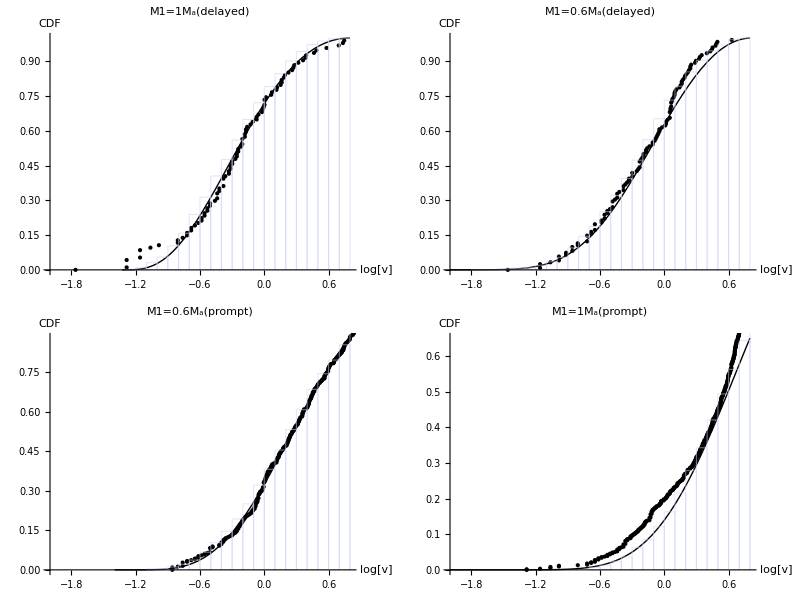

```mathematica
Grid@Partition[Table[Show[{Plot[Newfun[[i]],{x,-2,0.8},PlotStyle->Black],ListPlot[transepsdata[[i]],PlotStyle->Black],Histogram[Log10[testdist[[i]]],{0.1},"CDF",ChartStyle->{Opacity[0]}]},AxesLabel->{"log[v]","CDF"},PlotLabel->label[[i]],AxesOrigin->{-2,0},ImageSize->300],{i,4}],2]
```

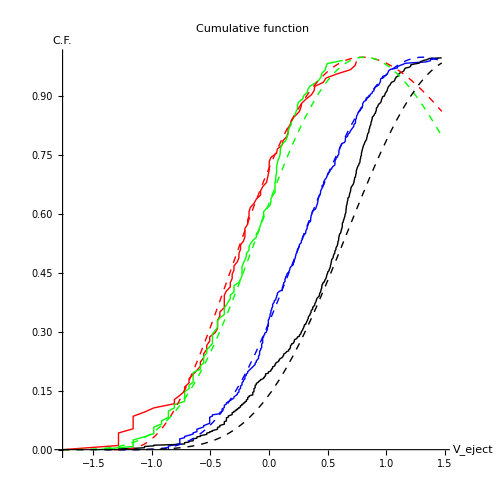

```mathematica
clr={Red,Green,Blue,Black};
Needs["PlotLegends`"];
epsdataplot=ListPlot[transepsdata,
PlotStyle->clr,AspectRatio->1,Joined->True,ImageSize->500,AxesLabel->{"V_eject","C.F."},PlotLabel->"Cumulative function",
PlotLegend->{"M1=1M_a(delayed)","M1=0.6M_a(delayed)","M1=0.6M_a(prompt)","M1=1M_a(prompt)"},LegendPosition->{0.8,0},LegendSize->{0.6,0.3},
LegendShadow->None,AxesOrigin->{Min@transepsdata[[All,All,1]],Min@transepsdata[[All,All,2]]},
Epilog->First@Show[Table[Plot[Newfun[[i]],{x,Min@transepsdata[[All,All,1]],Max@transepsdata[[All,All,1]]},
PlotStyle->{clr[[i]],Dashed}],{i,4}]]]
```

## Export

```mathematica
Export["/home/LWang/src/Nbody/Nbody6_new/info/Veject.PDF",Grid@{{Fittable},{epsdataplot},{"Fit function: smfun[x]:=d+10^a*(x-x0)^b*Exp[-(x-x0)/10^τ]"},{Anotherfit}}]
```

/home/LWang/src/Nbody/Nbody6_new/info/Veject.PDF

# Others